This notebook imports dat files, and plots energy eigenvalues of projected QAHI

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[dataEnergyPBC]
```

```mathematica
(** Change the filenames accordingly and import the dat files **)
```

```mathematica
dataEnergyPBC=Import["EigenvaluesParent60DislocationIrrational12to14mbyt0=2PBC.dat"];
```

```mathematica
npts = Dimensions[dataEnergyPBC][[1]]
```

316

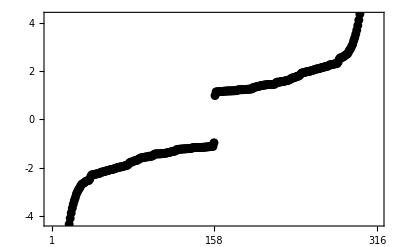

```mathematica
Show[
ListPlot[dataEnergyPBC,Frame-> True,Axes-> False,PlotRange-> {Automatic,{-4.25,4.25}},PlotStyle-> {Black,PointSize[0.016]},FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},FrameTicks-> {{{-4,-2,0,2,4},None},{{1,npts/2,npts},None}},
BaseStyle-> 18]
]
```